```mathematica
Do[
v=7;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];


Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];


Ch4[v][l]=Chi[v][l];
Cht4[v][l]=Chit[v][l];


i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

,{l,{2,5,10,20,40,60,80,100}}]
```

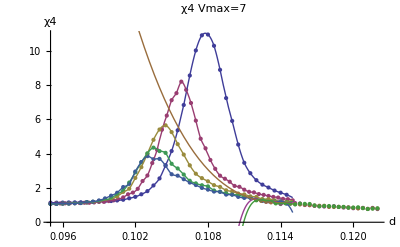

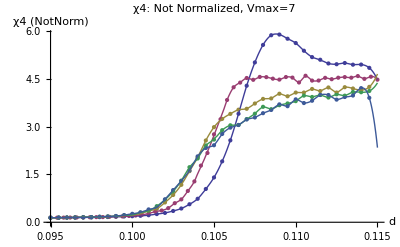

```mathematica
v=7;
pic1=ListPlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40],Ch4[v][60],Ch4[v][80],Ch4[v][100]},PlotRange->Full,PlotLabel->"χ4 Vmax=7",AxesLabel->{"d","χ4"}];
pic2=Plot[{i4[v][2][i],i4[v][5][i],i4[v][10][i],i4[v][20][i],i4[v][40][i],i4[v][60][i],i4[v][80][i],i4[v][100][i]},{i,0.095,0.115},PlotRange->Full];
pic3=ListPlot[{Cht4[v][2],Cht4[v][5],Cht4[v][10],Cht4[v][20],Cht4[v][40]},PlotRange->Full,PlotLabel->"χ4: Not Normalized, Vmax=7",AxesLabel->{"d","χ4 (NotNorm)"}];
pic4=Plot[{it4[v][2][i],it4[v][5][i],it4[v][10][i],it4[v][20][i],it4[v][40][i]},{i,0.095,0.115},PlotRange->Full];
Show[{pic1,pic2}]
Show[{pic3,pic4}]
```

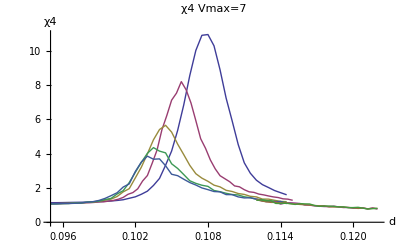

```mathematica
ListLinePlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40],Ch4[v][60],Ch4[v][80],Ch4[v][100]},PlotRange->Full,PlotLabel->"χ4 Vmax=7",AxesLabel->{"d","χ4"}]
```

```mathematica
Ch4[v][100]
```

{{0.112,1.28091},{0.1124,1.30147},{0.1128,1.25095},{0.1132,1.25112},{0.1136,1.09989},{0.114,1.09291},{0.1144,1.10907},{0.1148,1.08707},{0.1152,1.03965},{0.1156,1.08737},{0.116,1.07194},{0.1164,1.06539},{0.1168,0.979888},{0.1172,0.927161},{0.1176,0.945947},{0.118,0.94541},{0.1184,0.929217},{0.1188,0.893871},{0.1192,0.897021},{0.1196,0.850424},{0.12,0.855628},{0.1204,0.871907},{0.1208,0.822482},{0.1212,0.771771},{0.1216,0.79454},{0.122,0.810588}}